```mathematica
r1[s_]=Infinity;
```

## EQUAZIONI MIE

#### Equazioni di congruenza

```mathematica
ϵm4[s_]=0;
φ4[s_]=v4'[s];
κm4[s_]=φ4'[s];
ϵp4[s_]=v4[s]/r2[s];
```

#### Legame

```mathematica
Nm4[s_]=EA ϵm4[s]+ν EA ϵp4[s];
```

```mathematica
Tm4[s_]=-Mm4'[s];
```

```mathematica
Mm4[s_]=El κm4[s];
```

```mathematica
Np4[s_]=EA ϵp4[s]+ν EA ϵm4[s];
```

#### Equilibrio

```mathematica
EQ1=-Nm4'[s]-Tm4[s]/r1[s]==pt[s];
```

```mathematica
EQ2=Nm4[s]/r1[s]-Tm4'[s]+Np4[s]/r2[s]==pn[s]
```

(EA v4[s])/r2[s]^2+El v4^(4)[s]==pn[s]

```mathematica
(*L'equazione di campo ottenuta è molto semplice e formalmente simile a quella di un guscio cilindrico*)
```

```mathematica
r2[s_]=(R-s Cos[θ])/Sin[θ];
```

## EQUAZIONI REISSNER CONO

#### Equazioni di congruenza

```mathematica
ϵm[s_]=0;
φ[s_]=v'[s];
κm[s_]=φ'[s];
ϵp[s_]=(v[s]Sin [θ])/r0[s];
κp[s_]=(φ[s] Cos[θ])/r0[s];
```

#### Legame

```mathematica
Nm[s_]= EA ϵm[s]+ν EA ϵp[s];
```

```mathematica
(*Tm[s_]=5/6 G h γm[s];*)
Tm[s_]=-D[Mm[s] r0[s],s]/r0[s]+(Mp[s] Cos[θ])/r0[s];
```

```mathematica
Mm[s_]=El κm[s]+ν El κp[s];
```

```mathematica
Np[s_]= ν EA ϵm[s]+EA ϵp[s];
```

```mathematica
Mp[s_]=ν El κm[s]+El κp[s];
```

#### Equilibrio

```mathematica
EQ3=-D[Nm[s] r0[s],s]-Np[s] Cos[θ]==pt[s] r0[s];
EQ4=-D[Tm[s] r0[s],s]+Np[s] Sin[θ]==pn[s] r0[s];
```

```mathematica
EQUA={EQ4}
```

{(EA Sin[θ]^2 v[s])/r0[s]-r0'[s] ((Cos[θ] ((El Cos[θ] v'[s])/r0[s]+El ν v''[s]))/r0[s]+(-r0'[s] ((El ν Cos[θ] v'[s])/r0[s]+El v''[s])-r0[s] (-(El ν Cos[θ] r0'[s] v'[s])/r0[s]^2+(El ν Cos[θ] v''[s])/r0[s]+El v^(3)[s]))/r0[s])-r0[s] (-(Cos[θ] r0'[s] ((El Cos[θ] v'[s])/r0[s]+El ν v''[s]))/r0[s]^2+(Cos[θ] (-(El Cos[θ] r0'[s] v'[s])/r0[s]^2+(El Cos[θ] v''[s])/r0[s]+El ν v^(3)[s]))/r0[s]-(r0'[s] (-r0'[s] ((El ν Cos[θ] v'[s])/r0[s]+El v''[s])-r0[s] (-(El ν Cos[θ] r0'[s] v'[s])/r0[s]^2+(El ν Cos[θ] v''[s])/r0[s]+El v^(3)[s])))/r0[s]^2+1/r0[s](-r0''[s] ((El ν Cos[θ] v'[s])/r0[s]+El v''[s])-2 r0'[s] (-(El ν Cos[θ] r0'[s] v'[s])/r0[s]^2+(El ν Cos[θ] v''[s])/r0[s]+El v^(3)[s])-r0[s] ((2 El ν Cos[θ] r0'[s]^2 v'[s])/r0[s]^3-(El ν Cos[θ] v'[s] r0''[s])/r0[s]^2-(2 El ν Cos[θ] r0'[s] v''[s])/r0[s]^2+(El ν Cos[θ] v^(3)[s])/r0[s]+El v^(4)[s])))==pn[s] r0[s]}

```mathematica
(*L'equazione di campo ottenuta è molto più complessa*)
```

```mathematica
Collect[EQ4,{v[s],v'[s],v''[s],v'''[s],v''''[s]}]
```

(EA Sin[θ]^2 v[s])/r0[s]+(El Cos[θ]^2 r0'[s] v'[s])/r0[s]^2+(-(El Cos[θ]^2)/r0[s]+El r0''[s]) v''[s]+2 El r0'[s] v^(3)[s]+El r0[s] v^(4)[s]==pn[s] r0[s]

## SOLUZIONE EQUAZIONI

## DATI

```mathematica
h=0.2;
ν=0.2;
L=20;
L0=4;
R=L*Cos[θ]
EL=3×10^7;
γ=25;
p=-γ*h;
pn[s_]=p Cos[θ] ;
pt[s_]=p Sin[θ];
El=(EL h^3)/(12(1-ν^2));
EA=(EL h)/(1-ν^2);
G=EL/(2(1+ν));
θ=π/3;
```

20 Cos[θ]

```mathematica
r0[s_]=R-s Cos[θ];
```

```mathematica
EQ2=Nm4[s]/r1[s]-Tm4'[s]+Np4[s]/r2[s]==pn[s]
```

0.+(4.6875×10^6 v4[s])/(10-s/2)^2+20833.3 v4^(4)[s]==-2.5

```mathematica
EQUA={EQ2};
```

```mathematica
SOLA=NDSolve[{EQUA,v4[0]==0,φ4[0]==0,Tm4[L-L0]==0,Mm4[L-L0]==0},{u4,v4},{s,0,L-L0},WorkingPrecision ->30 , PrecisionGoal-> 10]
```

NDSolve::precw: The precision of the differential equation ({0.`  + 4.6875`*^6 v4[s]/(10 + « 1 »)^2 + 20833.33333333334` SuperscriptBox[« 3 »{}) is less than WorkingPrecision (30.).

NDSolve::berr: There are significant errors {1.85293626816851627119713687185×10^-71, -« 74 », -« 75 », « 74 »} in the boundary value residuals. Returning the best solution found.

{{u4→u4,v4→InterpolatingFunction[{{0,16.}},<>]}}

#### Spostamenti

```mathematica
u4[s_]=u4[s]/.SOLA;
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

```mathematica
v4[s_]=v4[s]/.SOLA;
```

```mathematica
φ4[s_]=φ4[s]/.SOLA;
```

#### Tensioni

```mathematica
Nm4[s_]=Nm4[s]/.SOLA;
```

```mathematica
Tm4[s_]=Tm4[s]/.SOLA;
```

```mathematica
Mm4[s_]=Mm4[s]/.SOLA;
```

```mathematica
Np4[s_]=Np4[s]/.SOLA;
```

```mathematica
Mp4[s_]=Mp4[s]/.SOLA;
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

```mathematica
A1=Plot[u4[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","u2(s)"},PlotStyle->{Orange,Thick},PlotRange->All];
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

```mathematica
A2=Plot[v4[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","v2(s)"},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
A3=Plot[φ4[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","φ2(s)"},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
A4=Plot[Nm4[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Nm2(s)"},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
A5=Plot[Np4[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Np2(s)"},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
A6=Plot[Tm4[s],{s,0.1,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Tm2(s)"},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
A7=Plot[Mm4[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Mm2(s)"},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
EQ4=-D[Tm[s] r0[s],s]+Np[s] Sin[θ]==pn[s] r0[s];
```

```mathematica
EQUA={EQ4};
```

```mathematica
SOLA=NDSolve[{EQUA,v[0]==0,φ[0]==0,Mm[L-L0]==0,Tm[L-L0]==0},{v},{s,0,L-L0},WorkingPrecision ->30 , PrecisionGoal-> 10]
```

NDSolve::precw: The precision of the differential equation ({{« 1 »}, {}, {}, {}, {}}) is less than WorkingPrecision (30.).

NDSolve::berr: There are significant errors {2.70137557151169887700238592232×10^-72, -« 74 », -« 76 », « 77 »} in the boundary value residuals. Returning the best solution found.

{{v→InterpolatingFunction[{{0,16.}},<>]}}

#### Spostamenti

```mathematica
u[s_]=u[s]/.SOLA;
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

```mathematica
v[s_]=v[s]/.SOLA;
```

```mathematica
φ[s_]=φ[s]/.SOLA;
```

#### Deformazioni

```mathematica
ϵm[s_]=ϵm[s]/.SOLA;
```

```mathematica
γm[s_]=γm[s]/.SOLA;
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

```mathematica
κm[s_]=κm[s]/.SOLA;
```

```mathematica
ϵp[s_]=ϵp[s]/.SOLA;
```

```mathematica
κp[s_]=κp[s]/.SOLA;
```

#### Tensioni

```mathematica
Nm[s_]=Nm[s]/.SOLA;
```

```mathematica
Tm[s_]=Tm[s]/.SOLA;
```

```mathematica
Mm[s_]=Mm[s]/.SOLA;
```

```mathematica
Np[s_]=Np[s]/.SOLA;
```

```mathematica
Mp[s_]=Mp[s]/.SOLA;
```

```mathematica
G1=Plot[u[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","u2(s)"},PlotStyle->{Black,Dashed},PlotRange->All];
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

```mathematica
G2=Plot[v[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","v2(s)"},PlotStyle->{Black,Dashed},PlotRange->All];
```

```mathematica
G3=Plot[φ[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","φ2(s)"},PlotStyle->{Black,Dashed},PlotRange->All];
```

```mathematica
G4=Plot[Nm[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Nm2(s)"},PlotStyle->{Black,Dashed},PlotRange->All];
```

```mathematica
G5=Plot[Np[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Np2(s)"},PlotStyle->{Black,Dashed},PlotRange->All];
```

```mathematica
G6=Plot[Tm[s],{s,0.1,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Tm2(s)"},PlotStyle->{Black,Dashed},PlotRange->All];
```

```mathematica
G7=Plot[Mm[s],{s,0,L-L0},AxesOrigin->{0,0},AxesLabel->{"s","Mm2(s)"},PlotStyle->{Black,Dashed},PlotRange->All];
```

## GRAFICI

### Spostamento u[s]

```mathematica
Show[A1,G1,PlotRange->All,PlotLabel->"Spostamento u(s)",AxesLabel->{"s","u(s)"},AxesOrigin->{0,0}];
```

### Spostamento v[s]

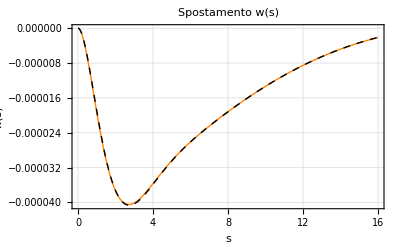

```mathematica
Show[A2,G2,PlotRange->All,PlotLabel->"Spostamento w(s)",AxesLabel->{"s","w(s)"},AxesOrigin->{0,0},GridLines->Automatic,Frame->True]
```

### Rotazione φ[s]

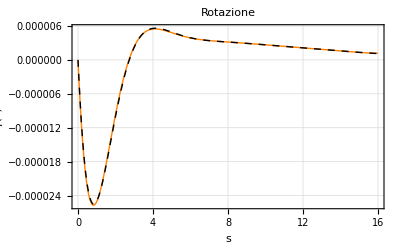

```mathematica
Show[A3,G3,PlotRange->All,PlotLabel->"Rotazione",AxesLabel->{"s","φ(s)"},AxesOrigin->{0,0},GridLines->Automatic,Frame->True]
```

### Taglio di meridiano Tm [s]

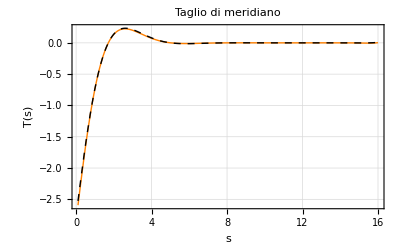

```mathematica
Show[A6,G6,PlotRange->All,PlotLabel->"Taglio di meridiano",AxesLabel->{"s","T(s)"},AxesOrigin->{0,0},GridLines->Automatic,Frame->True]
```

### Momento flettente di meridiano Mm [s]

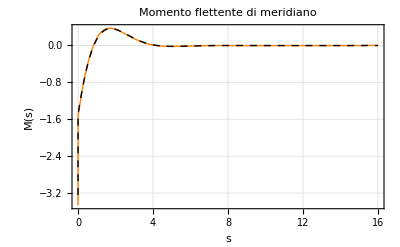

```mathematica
Show[A7,G7,PlotRange->All,PlotLabel->"Momento flettente di meridiano",AxesLabel->{"s","M(s)"},AxesOrigin->{0,0},GridLines->Automatic,Frame->True]
```

### Sforzo Normale di meridiano Nm[s]

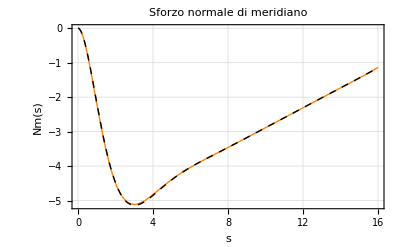

```mathematica
Show[A4,G4,PlotRange->All,PlotLabel->"Sforzo normale di meridiano",AxesLabel->{"s","Nm(s)"},AxesOrigin->{0,0},GridLines->Automatic,Frame->True]
```

### Sforzo Normale circonferenziale Nc[s]

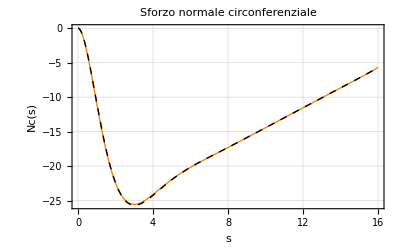

```mathematica
Show[A5,G5,PlotRange->All,PlotLabel->"Sforzo normale circonferenziale",AxesLabel->{"s","Nc(s)"},AxesOrigin->{0,0},GridLines->Automatic,Frame->True]
```